```mathematica
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)
x0 = 0;
y0 = 2;
v = 30;
th = 50*Pi/180;
vx0 = v*Cos[th];
vy0 = v*Sin[th]; 
vt = 35;

ode1={x''[t]==-(g x'[t]/vt^2)*Sqrt[x'[t]^2+y'[t]^2], x[0]== x0,x'[0]==vx0};
ode2={y''[t]==-g(l+(y'[t]/vt^2)*Sqrt[x'[t]^2+y'[t]^2]),y[0]==y0,y'[0]==vy0};
sol=NDSolve[{ode1, ode2},{x,y}, {t,0,200}];
```

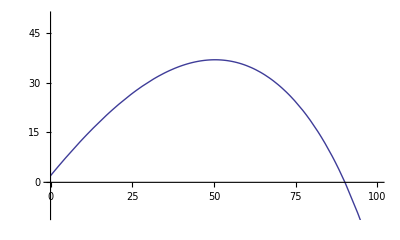

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t,0,200},PlotRange->{{0,100},{-10,50}}]
```

```mathematica
Manipulate[
g=9.8;l=0.5; 
x0 = 0;y0 = 2;

vx0 = v*Cos[th];
vy0 = v*Sin[th]; 

ode1={x''[t]==-(g x'[t]/vt^2)*Sqrt[x'[t]^2+y'[t]^2], x[0]== x0,x'[0]==vx0};
ode2={y''[t]==-g(l+(y'[t]/vt^2)*Sqrt[x'[t]^2+y'[t]^2]),y[0]==y0,y'[0]==vy0};

NDX = x0+v*Cos[th*t];
NDY = y0+v*Sin[th*t]-g*t^2/2;

Module[
{result = NDSolve[{ode1, ode2},{x,y}, {t,0,10}]},
ParametricPlot[{{x[t],y[t]}/.result,{NDX,NDY}/.result},{t,0,10},PlotRange->{{0,100},{-10,50}},PlotStyle-> {{Blue},{Red}},AxesLabel->{"x (m)","y (m)"},ImageSize->{500,300}]],
{{v,30,"initialvelocity (m/s)"},0,100,Appearance->"Labeled"},
{{th,50*Pi/180,"angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{vt,35,"terminal velocity (m/s)"},.1,100.,Appearance->"Labeled"},
{{qwe, 5.5,"time(s)"},0.,10., Appearance->"Labeled"}]
```